```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=8x + 12 y + x^2 - 2y^2;
Plot3D[f[x,y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
sol = Solve[D[f[x,y],{{x,y}}]== 0,{x,y},Reals]
jmat = D[f[x,y],{{x,y},2}]
Eigenvalues[jmat]/. sol
```

{{x→-4,y→3}}

{{2,0},{0,-4}}

{{-4,2}}

```mathematica
Plot3D[f[x,y],{x,-0.01,0.01},{y,-0.01,0.01}]
```

-Graphics3D-

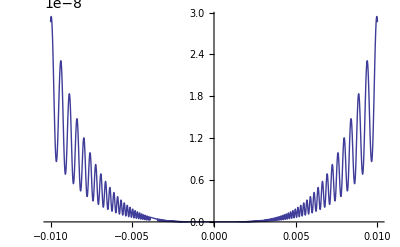

```mathematica
Clear[b]
b[x_]:= x^4 *Cos[1/x]+ 2x^4;
Plot[b[x],{x,-0.01,0.01}]
```

```mathematica
Clear[c]
c[z_,n_]:=Sum[(-1)^(2m+1)*z^(2m+1)/(2m+1),{m,1,n}];
Plot[c[z,100],{z,0,2}]
```

-Graphics-

```mathematica
c[z,100]
```

z-z^3/3+z^5/5-z^7/7+z^9/9-z^11/11

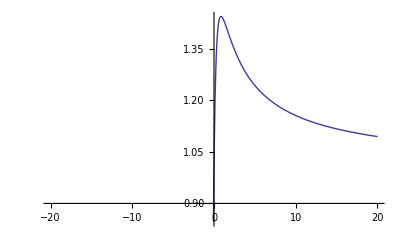

```mathematica
Plot[(2x+1)^(1/(2x+1)),{x,-20,20}]
```